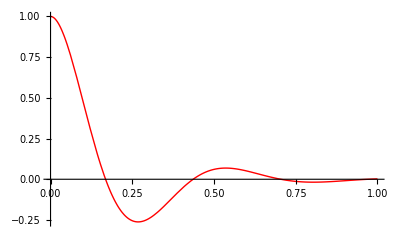

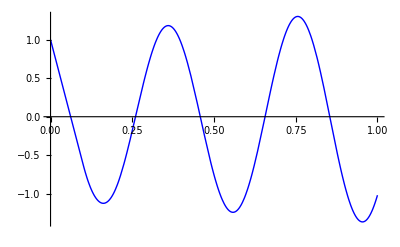

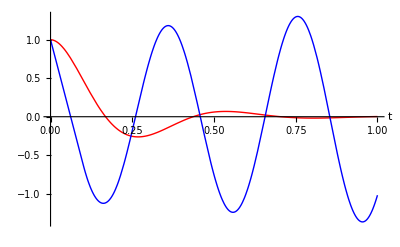

```mathematica
ClearAll;
a=1;
v=1;
k=4;
τ=0.1;
γ=v^2/(4*a^2)+a^2*k^2;
ft[x_[t_]]:=γ*x[t];
f[x_[t_]]:=(*(τ^3/6)*x''''[t]+(τ^2/2)*x'''[t]+*)τ*x''[t]+x'[t]+ft[x[t]];
g[x_[t_]]:=x'[t]+ft[x[t-τ]];
sol1=NDSolve[{f[x[t]]==0,x[0]==1,x'[0]==0},x,{t,0,1}];
sol2=NDSolve[{g[x[t]]==0,x[t/;t<0]==1},x,{t,0,1}];
p1:=Plot[Evaluate[x[t]/.sol1],{t,0,1},PlotStyle->Red,PlotRange->All];
p2:=Plot[Evaluate[x[t]/.sol2],{t,0,1},PlotStyle->Blue,PlotRange->All];
Show[p1]
Show[p2]
Show[{p1,p2},AxesLabel->{"t",""},PlotRange->All]
```